Last modified on: Tuesday, July 10, 2018 at 13:36

Author Info

Lawrence Temlock

Carl Woll

The Sun Exchange

Poster Session Content

Computing Text Reading Level

Train a neural network to recognize text reading level

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

Classical readability indices use counts of words, syllables, and word frequencies.  Recent systems such as Lexile leverage reading research and psychometric theory to score and match readers and books.   In this project, three approaches were used to test if a neural network can be trained to generate meaningful readability scores.  

Data was comprised of 97,000 text samples, 50-500 characters long, targeted with Lexile L-scores ranging from 430L (elementary) to 1350L (high school).  In Trial 1, sample text was assigned 100-column feature vectors via the The GloVe 100-Dimensional Word Vectors Trained on Wikipedia and Gigaword 5 Data (“GloVe Feature”), and input to an embedding layer in the network. Trial 2 solely input a 1-column word frequency vector; Trial 3 combined these two elements with NetEncoding. The common network architecture assembled two gated recurrent layers, followed by a sequence last layer and a linear layer.  

The result of Trial 1 was overfitting.  Trials 2 and 3 did not overfit, but both failed to reduce the output from the loss function. Random sample results from the networks compared unfavorably with those generated by the Dale-Challs Raw Score and Automated Readability Index.  The three network training trials were unable to produce networks capable of meaningfully scoring text reading level.

Future work can focus on (1) Cleaning data to remove unrepresentative text, (2) Lexile target alternatives, (3) diversifying text subject matter and reading difficulty, (4) longer net training, (5)  alternatives to the GloVe Feature, (6) sentence structure, parts of speech, and other inputs, (6) networks with more layers

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Section Header

Type text here

Section Header

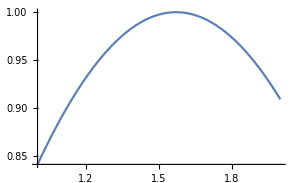
Plot[Sin[x],{x,1,2}]
-Graphics-

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

#### Main Results in Detail

#### Code

Provide one of:

Link to the GitHub

Explicit code

#### Written Content / Lesson Plans

#### Conclusions in Detail

#### All Visualizations

#### Data Sources Links/References

#### Future Directions

#### Background Info Links/References

#### Keywords

Provide keywords as items

< keyword 1 >

< keyword 2 >

#### Other information